```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3, 0≤x≤1}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3, 1<x≤2}, {c21(x-2)+c22(x-2)^2+c23(x-2)^3, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c01+c02+c03

c11+c12+c13

c21+c22+c23

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[f[x+2]+f[x+1]+f[x]+f[x-1]+f[x-2]+f[x-3],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[-2f[x+2]-f[x+1]+f[x-1]+2f[x-2]+3f[x-3],x>0&&x<1],x]
```

{2+c01+c02+c03+c11+c12+c13+c21+c22+c23,-2 c02-3 c03-2 c12-3 c13-2 c22-3 c23,2 c02+3 c03+2 c12+3 c13+2 c22+3 c23}

{1+c01+c02+c03+2 c11+2 c12+2 c13+3 c21+3 c22+3 c23,-c01-2 c02-3 c03-3 c11-4 c12-6 c13-5 c21-6 c22-9 c23,c02+3 c03+c12+6 c13+c22+9 c23,-c03-3 c13-5 c23}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0
	},
	{c01,c02,c03,c11,c12,c13,c21,c22,c23}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c03→-1-c01-c02,c13→-c11-c12,c21→-7/5-(7 c01)/5-(2 c02)/5-(6 c11)/5-c12/5,c22→6/5+(6 c01)/5+c02/5+(3 c11)/5-(2 c12)/5,c23→1/5+c01/5+c02/5+(3 c11)/5+(3 c12)/5}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0&&x<1&&y>0&&y<1],
	Simplify[SumF1,x>0&&x<1&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>3&&y<4]
}];
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1a6}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1a4,{{x,y}}]],
	FullSimplify[D[SumF1a5,{{x,y}}]],
	FullSimplify[D[SumF1a6,{{x,y}}]]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1&&x<2&&y>0&&y<1],
	Simplify[SumF1,x>1&&x<2&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-3&&y<-2]
}];
{DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5,DSumF1b6}=Parallelize[{
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
	FullSimplify[D[SumF1b4,{{x,y}}]],
	FullSimplify[D[SumF1b5,{{x,y}}]],
	FullSimplify[D[SumF1b6,{{x,y}}]]
}];
```

```mathematica
DSumF1a1=Simplify[DSumF1a1/.φ->1/2];
DSumF1a2=Simplify[DSumF1a2/.φ->1/2];
DSumF1a3=Simplify[DSumF1a3/.φ->1/2];
DSumF1a4=Simplify[DSumF1a4/.φ->1/2];
DSumF1a5=Simplify[DSumF1a5/.φ->1/2];
DSumF1a6=Simplify[DSumF1a6/.φ->1/2];
DSumF1b1=Simplify[DSumF1b1/.φ->1/2];
DSumF1b2=Simplify[DSumF1b2/.φ->1/2];
DSumF1b3=Simplify[DSumF1b3/.φ->1/2];
DSumF1b4=Simplify[DSumF1b4/.φ->1/2];
DSumF1b5=Simplify[DSumF1b5/.φ->1/2];
DSumF1b6=Simplify[DSumF1b6/.φ->1/2];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5,Err1a6}=Parallelize[{
	Simplify[∫_0^1 ∫_0^1 (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_0^1 (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_-1^0 (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-1^0 (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-2^-1 (DSumF1a5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_3^4 ∫_-2^-1 (DSumF1a6.{1,1})^2 ⅆxⅆy]
}];
{Err1b1,Err1b2,Err1b3,Err1b4,Err1b5,Err1b6}=Parallelize[{
	Simplify[∫_0^1 ∫_1^2 (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_1^2 (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_2^3 (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_2^3 (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_3^4 (DSumF1b5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-3^-2 ∫_3^4 (DSumF1b6.{1,1})^2 ⅆxⅆy]
}];
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1a6+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5+Err1b6];
```

```mathematica
Err=Err1
DErr=FullSimplify[D[Err,{{c01,c02,c11,c12}}]];
H=FullSimplify[D[Err,{{c01,c02,c11,c12},2}]];
```

1/63000000(168920343 c01^4+2150743 c02^4+c02^3 (39247427+11652126 c11+4020801 c12)+3 c01^3 (338365884+75342324 c02+102576067 c11+34569742 c12)+3 c02^2 (86246666+9448279 c11^2+c12 (19003966+1129579 c12)+c11 (53849841+6446208 c12))+3 c01^2 (743772216+37897886 c02^2+472541241 c11+83257779 c11^2+163357766 c12+56304408 c11 c12+9728279 c12^2+c02 (342228127+103130826 c11+35011901 c12))+3 c01 (681031404+8495924 c02^3+9 c11 (79014809+6 c11 (4732732+630747 c11))+251022806 c12+2 c11 (87948503+17271132 c11) c12+2 (15597639+5912207 c11) c12^2+1367488 c12^3+c02^2 (115746802+34626301 c11+11844926 c12)+2 c02 (252539891+4 c11 (39875404+6985551 c11)+55736941 c12+18966158 c11 c12+3293104 c12^2))+3 c02 (232270229+11409288 c11^3+c11^2 (87381503+11614814 c12)+c11 (241298906+44 c12 (1370699+90856 c12))+c12 (86575981+c12 (10688803+467138 c12)))+3 (222162041+11650551 c11^4+8 c11^3 (5500051+1964988 c12)+c11^2 (191553249+45408224 c12+8025506 c12^2)+c11 (337003107+2 c12 (67314799+7940562 c12+921752 c12^2))+3 c12 (40231594+c12 (8261833+c12 (624436+54117 c12)))))

```mathematica
NSols=NSolve[DErr==0,{c01,c02,c11,c12}];
TableForm[{Range[Length[NSols]],Err/.N[NSols],PositiveDefiniteMatrixQ[H/.N[#]]&/@NSols}ᵀ]
```

1 | 0.528298+7.33229 ⅈ | False
2 | 0.528298-7.33229 ⅈ | False
3 | 1.91013+4.95848 ⅈ | False
4 | 1.91013-4.95848 ⅈ | False
5 | 27.777-0.673146 ⅈ | False
6 | 27.777+0.673146 ⅈ | False
7 | 34.7981-9.52804 ⅈ | False
8 | 34.7981+9.52804 ⅈ | False
9 | 2.39764+1.73273 ⅈ | False
10 | 2.39764-1.73273 ⅈ | False
11 | 1.06742+1.6692 ⅈ | False
12 | 1.06742-1.6692 ⅈ | False
13 | 0.657+0.417678 ⅈ | False
14 | 0.657-0.417678 ⅈ | False
15 | 1.72704+0.121618 ⅈ | False
16 | 1.72704-0.121618 ⅈ | False
17 | 1.6985+0.11274 ⅈ | False
18 | 1.6985-0.11274 ⅈ | False
19 | 1.60671+0.174859 ⅈ | False
20 | 1.60671-0.174859 ⅈ | False
21 | -2.75266+2.23591 ⅈ | False
22 | -2.75266-2.23591 ⅈ | False
23 | 0.976594-0.041467 ⅈ | False
24 | 0.976594+0.041467 ⅈ | False
25 | 0.81858-0.432571 ⅈ | False
26 | 0.81858+0.432571 ⅈ | False
27 | 0.0999374-0.0418618 ⅈ | False
28 | 0.0999374+0.0418618 ⅈ | False
29 | 1.0239-0.14209 ⅈ | False
30 | 1.0239+0.14209 ⅈ | False
31 | 0.750415+0.396665 ⅈ | False
32 | 0.750415-0.396665 ⅈ | False
33 | 1.1604-0.139167 ⅈ | False
34 | 1.1604+0.139167 ⅈ | False
35 | 0.757358+0.5026 ⅈ | False
36 | 0.757358-0.5026 ⅈ | False
37 | 1.04765-0.378955 ⅈ | False
38 | 1.04765+0.378955 ⅈ | False
39 | 0.105569-0.0443054 ⅈ | False
40 | 0.105569+0.0443054 ⅈ | False
41 | 1.13148+0.0676579 ⅈ | False
42 | 1.13148-0.0676579 ⅈ | False
43 | 0.715452-0.262095 ⅈ | False
44 | 0.715452+0.262095 ⅈ | False
45 | 0.849866-0.351532 ⅈ | False
46 | 0.849866+0.351532 ⅈ | False
47 | 0.768947+0.381592 ⅈ | False
48 | 0.768947-0.381592 ⅈ | False
49 | 0.13038-0.0285524 ⅈ | False
50 | 0.13038+0.0285524 ⅈ | False
51 | 1.31338+0.124248 ⅈ | False
52 | 1.31338-0.124248 ⅈ | False
53 | 0.90527-0.0317635 ⅈ | False
54 | 0.90527+0.0317635 ⅈ | False
55 | 0.828893+0.144463 ⅈ | False
56 | 0.828893-0.144463 ⅈ | False
57 | 1.21393-0.161239 ⅈ | False
58 | 1.21393+0.161239 ⅈ | False
59 | 0.584939+0.0269389 ⅈ | False
60 | 0.584939-0.0269389 ⅈ | False
61 | 1.42522-0.269396 ⅈ | False
62 | 1.42522+0.269396 ⅈ | False
63 | 1.22402+0.213994 ⅈ | False
64 | 1.22402-0.213994 ⅈ | False
65 | 1.65848+0.552046 ⅈ | False
66 | 1.65848-0.552046 ⅈ | False
67 | 0.87112-0.232836 ⅈ | False
68 | 0.87112+0.232836 ⅈ | False
69 | 26.2029+8.75896 ⅈ | False
70 | 26.2029-8.75896 ⅈ | False
71 | 1.00509-0.246774 ⅈ | False
72 | 1.00509+0.246774 ⅈ | False
73 | 0.858078-0.750702 ⅈ | False
74 | 0.858078+0.750702 ⅈ | False
75 | 0.937562+0.371323 ⅈ | False
76 | 0.937562-0.371323 ⅈ | False
77 | 0.934118+0.349618 ⅈ | False
78 | 0.934118-0.349618 ⅈ | False
79 | 0.188007+0.00855673 ⅈ | False
80 | 0.188007-0.00855673 ⅈ | False
81 | 0.0295579 | True

```mathematica
Sols=Solve[DErr==0,{c01,c02,c11,c12}];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.0295579 | True
2 | 0.904847-10.8784 ⅈ | False
3 | 0.904847+10.8784 ⅈ | False
4 | 1.42522-0.269396 ⅈ | False
5 | 1.42522+0.269396 ⅈ | False
6 | 1.21393-0.161239 ⅈ | False
7 | 1.21393+0.161239 ⅈ | False
8 | 0.188007+0.00855673 ⅈ | False
9 | 0.188007-0.00855673 ⅈ | False
10 | 1.22402+0.213994 ⅈ | False
11 | 1.22402-0.213994 ⅈ | False
12 | 4.72904+5.11114 ⅈ | False
13 | 4.72904-5.11114 ⅈ | False
14 | 0.899583-0.735862 ⅈ | False
15 | 0.899583+0.735862 ⅈ | False
16 | 30.5054+94.4651 ⅈ | False
17 | 30.5054-94.4651 ⅈ | False
18 | -2.75266-2.23591 ⅈ | False
19 | -2.75266+2.23591 ⅈ | False
20 | -22.9962+12.9345 ⅈ | False
21 | -22.9962-12.9345 ⅈ | False
22 | 174.667-52.7064 ⅈ | False
23 | 174.667+52.7064 ⅈ | False
24 | -192.099+70.049 ⅈ | False
25 | -192.099-70.049 ⅈ | False
26 | -8.45113-17.1864 ⅈ | False
27 | -8.45113+17.1864 ⅈ | False
28 | -83.4379+50.3345 ⅈ | False
29 | -83.4379-50.3345 ⅈ | False
30 | -7.71688-20.003 ⅈ | False
31 | -7.71688+20.003 ⅈ | False
32 | -5.31714×10^14+3.04748×10^14 ⅈ | False
33 | -5.31714×10^14-3.04748×10^14 ⅈ | False
34 | -202.856+84.5498 ⅈ | False
35 | -202.856-84.5498 ⅈ | False
36 | 290.694+2422.67 ⅈ | False
37 | 290.694-2422.67 ⅈ | False
38 | -5.88089×10^8+5.91726×10^9 ⅈ | False
39 | -5.88089×10^8-5.91726×10^9 ⅈ | False
40 | -470.259+339.438 ⅈ | False
41 | -470.259-339.438 ⅈ | False
42 | -5.99938×10^10+5.04895×10^12 ⅈ | False
43 | -5.99938×10^10-5.04895×10^12 ⅈ | False
44 | -372.009+3525.32 ⅈ | False
45 | -372.009-3525.32 ⅈ | False
46 | -122.439-245.574 ⅈ | False
47 | -122.439+245.574 ⅈ | False
48 | -544.074-98.1515 ⅈ | False
49 | -544.074+98.1515 ⅈ | False
50 | 108.599-159.312 ⅈ | False
51 | 108.599+159.312 ⅈ | False
52 | -854.48+108.168 ⅈ | False
53 | -854.48-108.168 ⅈ | False
54 | -694.859-70.2148 ⅈ | False
55 | -694.859+70.2148 ⅈ | False
56 | -59.5842-390.921 ⅈ | False
57 | -59.5842+390.921 ⅈ | False
58 | -6.71817×10^15+1.38041×10^15 ⅈ | False
59 | -6.71817×10^15-1.38041×10^15 ⅈ | False
60 | -2.92834×10^48+2.53342×10^48 ⅈ | False
61 | -2.92834×10^48-2.53342×10^48 ⅈ | False
62 | -294.521-486.566 ⅈ | False
63 | -294.521+486.566 ⅈ | False
64 | -2817.03+1406.07 ⅈ | False
65 | -2817.03-1406.07 ⅈ | False
66 | 167.009-566.413 ⅈ | False
67 | 167.009+566.413 ⅈ | False
68 | 978.143-428.3 ⅈ | False
69 | 978.143+428.3 ⅈ | False
70 | 233.846-1362.21 ⅈ | False
71 | 233.846+1362.21 ⅈ | False
72 | -6227.23-5696.33 ⅈ | False
73 | -6227.23+5696.33 ⅈ | False
74 | 598.76-8702.26 ⅈ | False
75 | 598.76+8702.26 ⅈ | False
76 | -6084.41-34503.9 ⅈ | False
77 | -6084.41+34503.9 ⅈ | False
78 | -1.13217×10^55+5.58864×10^54 ⅈ | False
79 | -1.13217×10^55-5.58864×10^54 ⅈ | False
80 | -5.47206×10^50+1.02241×10^51 ⅈ | False
81 | -5.47206×10^50-1.02241×10^51 ⅈ | False

{c03→0.188667,c13→0.1685946,c21→0.0925784,c22→0.0463118,c23→-0.13889,c01→-0.4353302219,c02→-0.753337,c11→-0.548062449,c12→0.37946786}

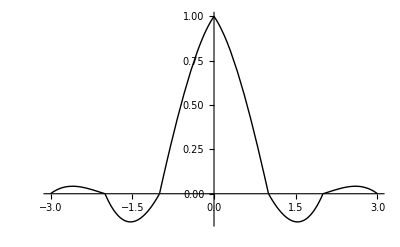

```mathematica
Sol=Sols[[1]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```